```mathematica
ClearAll["Global`*"];
```

```mathematica
SetOptions[Plot3D,ImageSize->800]; SetOptions[Plot,ImageSize->800];
SetOptions[ContourPlot,ImageSize->800]; SetOptions[ListPlot,ImageSize->800];
SetOptions[ParametricPlot,ImageSize->800];
```

```mathematica
ω = 0.0228;
ℰ = 0.0655;
Ip = 0.579; 

n=36;
A[t_] = (ℰ/ω)Cos[ω t/(2n)]^2 Cos[ω t];
F[t_] = Integrate[A[t],t];
Ε[t_] = -A'[t];
```

```mathematica
endMomentumNum[v0_,t0d_] := Module[{t0=2π t0d/(360ω)},
tend= n  π/ω;
acc = 0.001;
(* coulomb force *)
fcx[x_,y_] := -x/(x^2 + y^2 + acc^2)^(3/2);
fcy[x_,y_] := -y/(x^2 + y^2 + acc^2)^(3/2);
(* motion with Coulomb force *)
trajectC = NDSolve[{
		x''[t] == -Ε[t] + fcx[x[t],y[t]],
		y''[t] == fcy[x[t],y[t]],
		x[t0] == -Ip/Ε[t0],
		y[t0] == 0,
		x'[t0] == 0,
		y'[t0] == v0
	},
	{x, y},
	{t, t0, tend},
	MaxSteps->40000
];
endEnergy = First@(((x'[tend]^2+ y'[tend]^2)/2 -1/(x[tend]^2+ y[tend]^2)^(1/2))/.trajectC);
res[e_?Positive] := First@({x'[tend], y'[tend]}/.trajectC);
res[e_?NonPositive] := {Null,Null};
res[endEnergy]
(*First@({x'[tend], y'[tend]}/.trajectC)*)
(*First@(((x'[tend]^2+ y'[tend]^2)/2 -1/(x[tend]^2+ y[tend]^2)^(1/2))/.trajectC)*)
]
```

```mathematica
filterRow=Function[{row},
rev = Reverse[row];
pairs = Partition[rev,2,1];
mask = Map[ (Norm[Last[#]-First[#]]<=0.1)&,pairs];
falsePos = Position[mask,False];
offset = If[falsePos == {}, Length[row]+1,falsePos[[1,1]]];
Reverse[Take[rev, offset-1]]
];
```

```mathematica
globalPlotNum1 = ParallelTable[
endMomentumNum[v0,t0],
{v0,0.005,0.20, 0.01},
{t0,75,105,0.25}
];
```

$Aborted

```mathematica
globalPlotNumForbidden = ParallelTable[
endMomentumNum[v0,t0],
{v0,0.036,0.046, 0.001},
{t0,75,99.5,0.05}
];
```

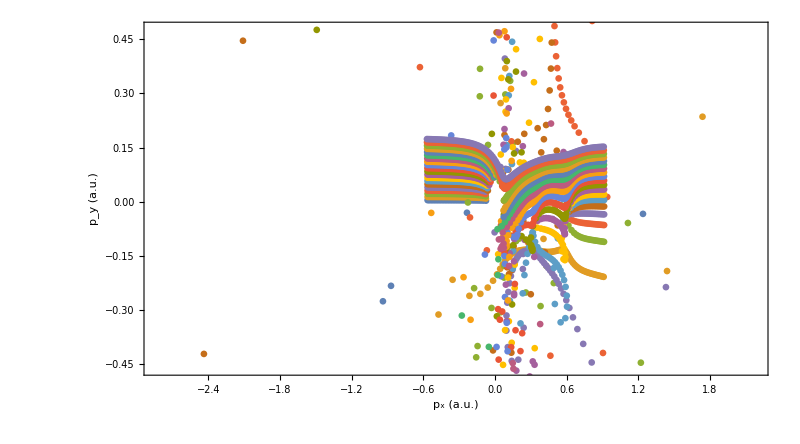

```mathematica
p1 = ListPlot[
globalPlotNum1,
(*PlotRange->{{-1,1},{-0.25,0.25}},*)
FrameLabel-> { "p_x (a.u.)","p_y (a.u.)"},
AxesStyle->Directive[Black,FontSize->14],
AspectRatio -> 1/1.8,
PlotStyle->(PointSize[0.006]),
(*Axes->False,*)
Frame->{True,True,True,True},
FrameTicksStyle->Directive[FontSize->14],
FrameStyle->Directive[FontSize->14]
]
```

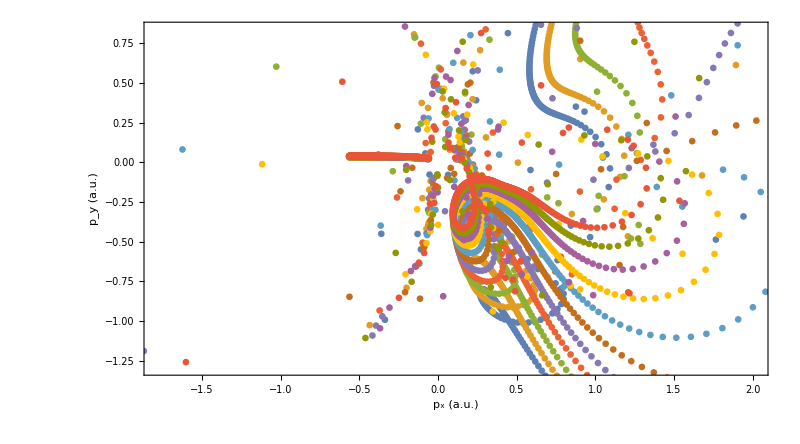

```mathematica
p2 = ListPlot[
globalPlotNumForbidden,
(*PlotRange->{{-1,1},{-0.25,0.25}},*)
FrameLabel-> { "p_x (a.u.)","p_y (a.u.)"},
AxesStyle->Directive[Black,FontSize->14],
AspectRatio -> 1/1.8,
PlotStyle->(PointSize[0.006]),
(*Joined -> True,*)
(*Axes->False,*)
Frame->{True,True,True,True},
FrameTicksStyle->Directive[FontSize->14],
FrameStyle->Directive[FontSize->14]
]
```

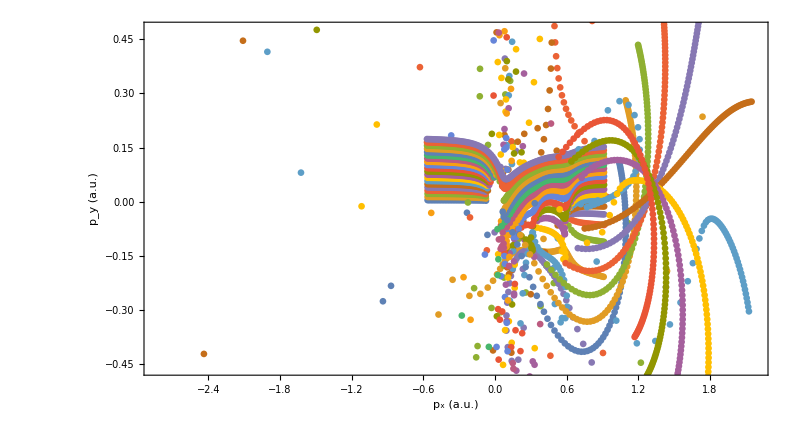

```mathematica
Show[p1,p2]
```